Here’s the fiberwise ODE — that is, the vector ODE representing the connection — produced by the notebook entitled threeLinkSwimmerWithSpringForceForJoeAndJack.nb, subject to the assumption that the three links are ellipses of the same size and shape, equally spaced in a particular way, and subject to some assumption about the density of the surrounding fluid.

```mathematica
originalFiberwiseODE =  fiberwiseODE /. ellipses /. equalGaps /. {aT -> a, aB -> a, aH -> a};
```

This system of ODEs can be rearranged to take the form

	x’[t] = a function of x, y, θ, η, τ, η’, τ’
	y’[t] = a function of x, y, θ, η, τ, η’, τ’
	θ’[t] = a function of x, y, θ, η, τ, η’, τ’

as follows:

```mathematica
originalODEx = Solve[originalFiberwiseODE, x'[t], {y'[t], θ'[t]}] // Simplify;
```

```mathematica
originalODEy = Solve[originalFiberwiseODE, y'[t], {x'[t], θ'[t]}] // Simplify;
```

```mathematica
originalODEθ = Solve[originalFiberwiseODE, θ'[t], {x'[t], y'[t]}] // Simplify;
```

The right-hand sides of these ODEs can be extracted thus:

```mathematica
originalRHSx = Part[x'[t] /. originalODEx, 1];
```

```mathematica
originalRHSy = Part[y'[t] /. originalODEy, 1];
```

```mathematica
originalRHSθ = Part[θ'[t] /. originalODEθ, 1];
```

Here's the ODE governing the behavior of the tail hinge under the same assumptions as those mentioned above.

```mathematica
originalTailHingeODE = tailHingeODE /. ellipses /. equalGaps /. {aT -> a, aB -> a, aH -> a};
```

That ODE includes not only x’[t], y’[t], and θ’[t] but also x’’[t], y’’[t], and θ’’[t]. To eliminate these quantities, we’ll need to replace the latter three with the time derivatives of the expressions originalRHSx, originalRHSy, and originalRHSθ, and then replace the former three with the expressions originalRHSx, originalRHSy, and originalRHSθ themselves. This process will result in a monstrously long expression for τ’’[t].

```mathematica
hideousEvaluation = Solve[originalTailHingeODE /. {x''[t] -> D[originalRHSx, t], y''[t] -> D[originalRHSy, t], θ''[t] -> D[originalRHSθ, t]} /. {x'[t] -> originalRHSx, y'[t] -> originalRHSy, θ'[t] -> originalRHSθ}, τ''[t]] ;
```

```mathematica
tailAcceleration = Part[τ''[t] /. hideousEvaluation, 1];
```

We want to replace the second-order ODE governing the dynamics of the tail with two first-order ODEs, so we should add the ODE

	τ’[t] = υ[t]
	
to our list of ODEs — so that now tailAcceleration = υ’[t] — and replace all instances of τ’[t] in all the ODEs above with instances of υ[t].

```mathematica
newRHSx = originalRHSx /. τ'[t] -> υ[t];
```

```mathematica
newRHSy = originalRHSy /. τ'[t] -> υ[t];
```

```mathematica
newRHSθ = originalRHSθ /. τ'[t] -> υ[t];
```

```mathematica
newRHSτ = υ[t];
```

```mathematica
newRHSυ = tailAcceleration /. τ'[t] -> υ[t];
```

We now have the system of first-order ODEs that Jack wants, though we’ll have to adjust their syntax to suit his purposes. Before making those adjustments — that is, before making the right-hand sides of the ODEs look like expressions in Python or MATLAB instead of expressions in the Wolfram language — let’s run a simulation to verify that we haven’t screwed something up.

We’ll let a = 7, k = 1000, c = 2000, and η[t] = Cos[t]. According to the previous notebook, this should generate behavior like this:

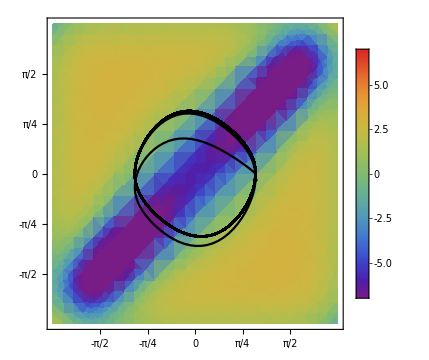
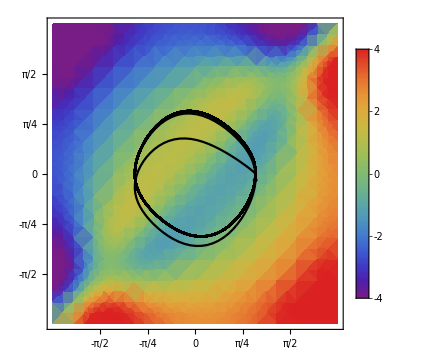
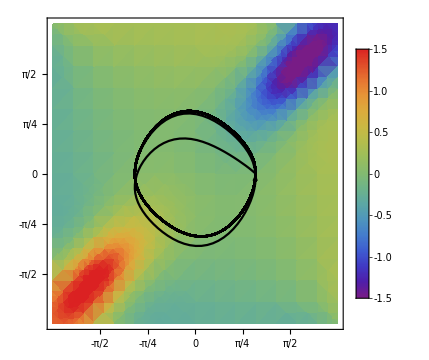
-Graphics- | -Graphics- | -Graphics-
displacement after first cycle = | final cycle phase =  | 
{8.26033,2.0114,0.120461} | {9.96663,2.75639,8.29662×10^-8} |

```mathematica
fullPathPlots[1, 1, 1000, 2000, 7, 7, 7]
```

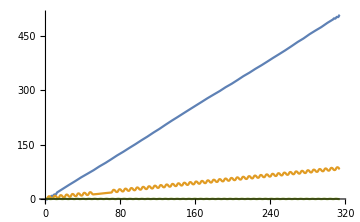
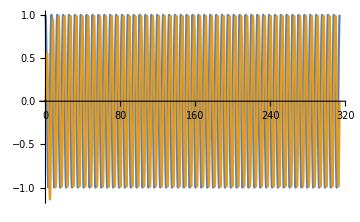
-Graphics- | -Graphics-

```mathematica
timePlots[1, 1, 1000, 2000, 7, 7, 7]
```

```mathematica
movie[1, 1, 1000, 2000, 7, 7, 7]
```

Okay, here goes.

```mathematica
newSolution = NDSolve[{x'[t] == newRHSx, y'[t] == newRHSy, θ'[t] == newRHSθ, τ'[t] == newRHSτ, υ'[t] == newRHSυ, x[0] == 0, y[0] == 0, θ[0] == 0, τ[0] == 0, υ[0] == 0} /. {a -> 7, k -> 1000, c -> 2000, η[t] -> Cos[t], η'[t] -> - Sin[t], η''[t] -> - Cos[t]}, {x[t], y[t], θ[t]}, {t, 0, 100 π}, Method->{"EquationSimplification"->"Residual"}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}}

Did we get the same simulation results as we would’ve gotten from the previous notebook?

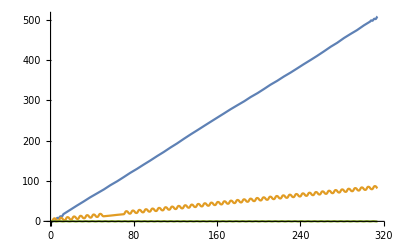

```mathematica
Plot[Evaluate[{x[t], y[t], θ[t]} /. newSolution], {t, 0, 100 π}]
```

We did! Okay, now we just have to Python-ify the syntax of the right-hand sides of our ODEs. First, let’s gather those right-hand sides into a list.

```mathematica
newRHS = {newRHSx, newRHSy, newRHSθ, newRHSτ, newRHSυ};
```

Next, let’s define a bunch of replacement rules to make the adjustments we want...

We want to get rid of the argument [t] following every symbolic variable name, and also rename the variables that are currently represented by Greek letters.

```mathematica
newVariables = {x[t] -> x, y[t] -> y, θ[t] -> tilt, τ[t] -> butt, υ[t] -> buttdot, η[t] -> neck, η'[t] -> neckdot, η''[t] -> neckddot};
```

We also want to replace Cos[ ] with cos( ) and replace Sin[ ] with sin( ), but we need to be careful about the fact that Mathematica will interpret regular parentheses like an ordinary person would. An expression like cos(2), if “cos” appears to be the name of a variable, is the same as 2 times “cos”, but we don’t want Mathematica making the substitution Cos[something] -> cos(something) -> cos*something. We’ll therefore resist applying a rule like Cos[anything_] -> cos(anything), and content ourselves with un-capitalizing the names of the functions as a first step.

```mathematica
trigChanges = {Cos -> cos, Sin -> sin};
```

We also want to introduce an * every time two things are multiplied together, and to replace every super-scripted exponent with an expression involving ^. These things can be achieved by piping everything through the InputForm command. If we take the result and convert it to a string, we can replace [ ] with ( ) thereafter without worrying that Mathematica will think it’s handling a mathematical expression.

If we feed the complete list of right-hand sides into InputForm, the result will no longer have the structure of a list: its Head will be InputForm rather than List. Let's therefore define a function that does what we just said to a single scalar entity, with the intention of distributing this function element-by-element over the list using /@.

```mathematica
fixTheSyntax :=  StringReplace[(#// InputForm // ToString), {"[" -> "(", "]" -> ")", "^" ->  "**"}] &
```

At last, here’s the list of right-hand-sides that Jack wants:

```mathematica
jackRHS = fixTheSyntax /@ (newRHS /. newVariables /. trigChanges);
```

Looking at this entire list at once would make us go blind, so we’ll just look at one of the shorter terms to admire our handiwork:

```mathematica
jackRHS[[3]]
```

(8*a^6*(3 + 2*a)^2*(-cos(butt) + cos(neck))*(buttdot*cos(butt) + neckdot*cos(neck))*((-209952 + 324*a^4 + a^8)*cos(butt) + (-209952 + 324*a^4 + a^8)*cos(neck) + a^4*(648 + a^4 + (-324 + a^4)*cos(butt + neck))) - (-((-324 + a^4)^2*buttdot) + (-324 + a^4)^2*neckdot - 4*a^6*(3 + 2*a)^2*buttdot*cos(butt/2)^2 + 4*a^6*(3 + 2*a)^2*neckdot*cos(neck/2)^2)*(4*(a^4 + a^4*cos(butt)^2 + a^4*cos(neck)^2 + 324*sin(butt)^2 + 324*sin(neck)^2)*(324 + 324*cos(butt)^2 + 324*cos(neck)^2 + a^4*sin(butt)^2 + a^4*sin(neck)^2) - (-324 + a^4)^2*(-sin(2*butt) + sin(2*neck))^2) + 4*a^6*(3 + 2*a)^2*(-(buttdot*sin(butt)) + neckdot*sin(neck))*(972*a^4*sin(butt) + 3*a^8*sin(butt) - 104976*sin(2*butt) - 324*a^4*sin(2*butt) + 2*a^8*sin(2*butt) + 3*a^4*(324 + a^4)*sin(neck) + 2*(-52488 - 162*a^4 + a^8)*sin(2*neck) + 104976*sin(2*(butt + neck)) - 648*a^4*sin(2*(butt + neck)) + a^8*sin(2*(butt + neck)) - 324*a^4*sin(2*butt + neck) + a^8*sin(2*butt + neck) - 324*a^4*sin(butt + 2*neck) + a^8*sin(butt + 2*neck)))/(-8*a^2*(3 + 2*a)^2*(-cos(butt) + cos(neck))^2*(a^4 + (-324 + a^4)*cos(butt) + (-324 + a^4)*cos(neck))*((-209952 + 324*a^4 + a^8)*cos(butt) + (-209952 + 324*a^4 + a^8)*cos(neck) + a^4*(648 + a^4 + (-324 + a^4)*cos(butt + neck))) + (5832*a^2 + 2592*a^3*(3 + a) + 6*a^6*(3 + 2*a)^2 + 3*(-324 + a^4)^2 + 24*a^7*cos(butt) + 4*a^6*(9 + 6*a + 4*a^2)*cos(butt) + a^2*(3 + 2*a)^2*(-324 + a^4)*cos(2*butt) + 4*a^6*(3 + 2*a)^2*cos(neck) + a^2*(3 + 2*a)^2*(-324 + a^4)*cos(2*neck))*(4*(a^4 + a^4*cos(butt)^2 + a^4*cos(neck)^2 + 324*sin(butt)^2 + 324*sin(neck)^2)*(324 + 324*cos(butt)^2 + 324*cos(neck)^2 + a^4*sin(butt)^2 + a^4*sin(neck)^2) - (-324 + a^4)^2*(-sin(2*butt) + sin(2*neck))^2) - 2*a^2*(3 + 2*a)^2*(2*(a^4 + (-324 + a^4)*cos(butt))*sin(butt) + 2*a^4*sin(neck) + (-324 + a^4)*sin(2*neck))*(972*a^4*sin(butt) + 3*a^8*sin(butt) - 104976*sin(2*butt) - 324*a^4*sin(2*butt) + 2*a^8*sin(2*butt) + 3*a^4*(324 + a^4)*sin(neck) + 2*(-52488 - 162*a^4 + a^8)*sin(2*neck) + 104976*sin(2*(butt + neck)) - 648*a^4*sin(2*(butt + neck)) + a^8*sin(2*(butt + neck)) - 324*a^4*sin(2*butt + neck) + a^8*sin(2*butt + neck) - 324*a^4*sin(butt + 2*neck) + a^8*sin(butt + 2*neck)))

We’ll export the entire list to a plain text file. To help Jack see where one right-hand side ends and the next begins in this file, I’d like to insert a blank line after each one except the last. I don’t know how to do this with the Export command, so I’ll use the Riffle command to insert an additional element, containing an empty string, between every two elements in jackRHS, and export the result of that operation.

```mathematica
Export["jackRHS.txt", Riffle[jackRHS, ""]]
```

jackRHS.txt

Done! So, to review:

The exported file jackRHS.txt contains a list of five expressions that depend on the symbols x, y, tilt, butt, buttdot, neck, neckdot, neckddot, a, k, and c. These expressions represent, in order, the rates of change of x, y, tilt, butt, and buttdot. Explicit functions of time need to be substituted in for neck, neckdot, and neckddot to represent the actuation applied to the swimmer’s forward joint, and numerical values need to be substituted in for a, k, and c to represent the semimajor axis of the ellipses comprising the swimmer, the stiffness of the tail joint, and the damping coefficient of the tail joint, respectively. Reasonable sample values are given earlier in this notebook.